# Logistic Map

### Author

Eric W. Weisstein
October 26, 2008

This notebook downloaded from http://mathworld.wolfram.com/notebooks/DynamicalSystems/LogisticMap.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/LogisticMap.html.

©2008 Wolfram Research, Inc. except for portions noted otherwise

### Additional Authors

Michael Trott

### Code

```mathematica
If[$VersionNumber<6.0,
Discriminant[p_?PolynomialQ,x_]:=With[{m=Exponent[p,x]},Cancel[((-1)^(1/2m(m-1))Resultant[p,D[p,x],x])/Coefficient[p,x,m]^(2m-1)]
]
]
```

```mathematica
CycleOnsetGroebner[n_Integer/;n>2,opts___?OptionQ]:=Module[{a=Array[x,n],r},
Evaluate[
GroebnerBasis[
Append[r #1(1-#1)-#2&@@@Partition[a,2,1,1],
r^n Times@@((1-2#)&/@a)-1],
r,a,opts,MonomialOrder->EliminationOrder][[1]]/.r->#]&
]

CycleOnset[1,opts___?OptionQ]:=1
CycleOnset[2,opts___?OptionQ]:=3
CycleOnset[n_Integer/;n>2,opts___?OptionQ]:=Min[x/.{ToRules[Reduce[CycleOnsetGroebner[n,opts][x]==0&&x>3,x]]}]
```

```mathematica
NCycleOnset[n_,opts___]:=Module[{a=Array[x,n],r},Select[Select[Union[r/.NSolve[
Append[r #1(1-#1)-#2&@@@Partition[a,2,1,1],
r^n Times@@( (1-2#)&/@a)-1],
r,a,opts]],Positive],#>3&]
]
```

```mathematica
NCycleMinimize[n_,opts___]:=Module[{a=Array[x,n],r},NMinimize[{r,
And@@Append[r #1(1-#1)==#2&@@@Partition[a,2,1,1],
r^n Times@@( (1-2#)&/@a)==1]&&3<r<4&&And@@(0<#<1&/@a)
},
Prepend[a,r],
opts
][[1]]
]
```

```mathematica
f[x_]:=r x(1-x)
```

## Web Diagram

```mathematica
LogisticSegments[r_,x0_,its_]:=Module[
{l=NestList[r#(1-#)&,x0,its]},
Partition[Flatten[Transpose[{l,l}]],2,1]
]
```

```mathematica
p2=Partition[LogisticSegments[3.741,.00079,15],2,1];
```

```mathematica
movie=Table[Plot[{3.741x(1-x),x},{x,0,1},PlotStyle->{{},Dashing[{.02}]},
Prolog->MapIndexed[{Hue[#2[[1]]/Length[p2]],Line[#]}&,Take[p2,i]],
AspectRatio->Automatic,
AxesLabel->TraditionalForm/@{Subscript[x, n],Subscript[x, n+1]}
],{i,Length[p2]}];
```

```mathematica
<<Utilities`GIF`;
```

```mathematica
Export[gifs<>"logistic.gif",movie]//Timing
```

{8.69 Second,/Volumes/Data/Troves/MathOzTeX/newgifs/logistic.gif}

```mathematica
movie=Table[Plot[{3.741x(1-x),x},{x,0,1},PlotStyle->{{},Dashing[{.02}]},
Prolog->MapIndexed[{Hue[#2[[1]]/Length[p2]],Line[#]}&,Take[p2,i]],
AspectRatio->Automatic,
AxesLabel->TraditionalForm/@{Subscript[x, n],Subscript[x, n+1]}
],{i,Length[p2]}];
```

```mathematica
ListAnimate[movie]
```

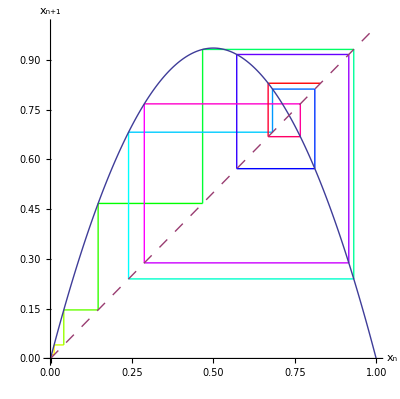

```mathematica
Last[movie]
```

## Iterations

```mathematica
Factor[Table[Nest[r#(1-#)&,x,n],{n,3}]]//TableForm//TraditionalForm
```

-r (x-1) x
-r^2 (x-1) x (r x^2-r x+1)
-r^3 (x-1) x (r x^2-r x+1) (r^3 x^4-2 r^3 x^3+r^3 x^2+r^2 x^2-r^2 x+1)

## Plots

```mathematica
Show[GraphicsArray[Partition[Table[
Plot[Evaluate[Table[Nest[r#(1-#)&,x,n],{n,5}]],{x,0,1},PlotRange->All,PlotStyle->{Red,Yellow,Green,Blue,Purple},AxesLabel->TraditionalForm/@{Subscript[x, 0],Subscript[x, n]},PlotLabel->TraditionalForm[HoldForm[r]==r],
DisplayFunction->Identity],
{r,4}],2]],ImageSize->500]
```

⁃GraphicsArray⁃

## Bifurcation Diagrams

```mathematica
LogisticMap=Compile[{{μ,_Real}},({μ,#}&)/@Union[Drop[NestList[μ # (1-#)&,.2,300],100]]];
```

```mathematica
f=Table[LogisticMap[μ],{μ,0,4,.002}];//Timing
```

{0.695292 Second,Null}

```mathematica
ListPlot[Flatten[f,1],
PlotStyle->{Red,AbsolutePointSize[.001]},Frame->True,
FrameLabel->TraditionalForm/@{r,x},PlotLabel->TraditionalForm[Subscript[x, n]==r Subscript[x, n-1](1-Subscript[x, n-1])]
]
```

⁃Graphics⁃

```mathematica
f=Table[LogisticMap[μ],{μ,1.0,4.0,.002}];//Timing
```

{0.9 Second,Null}

```mathematica
ListPlot[Flatten[f,1],
PlotStyle->{Red,AbsolutePointSize[.001]},Frame->True,
FrameLabel->TraditionalForm/@{r,x},PlotLabel->TraditionalForm[Subscript[x, n]==r Subscript[x, n-1](1-Subscript[x, n-1])]
]
```

⁃Graphics⁃

```mathematica
f=Table[LogisticMap[μ],{μ,3.44,3.58,.00005}];//Timing
```

{1.26 Second,Null}

```mathematica
ListPlot[Flatten[f,1],
PlotStyle->{Red,AbsolutePointSize[.001]},Frame->True,
FrameLabel->TraditionalForm/@{r,x},
Axes->False,PlotLabel->TraditionalForm[Subscript[x, n]==r Subscript[x, n-1](1-Subscript[x, n-1])],
Prolog->{{Blue,Line[{{#,0},{#,1}}]&/@{3.44949,3.544090,3.564407,3.56875,3.56969,3.56989,3.569934,3.569943,3.5699451,3.569945557,3.569945672}}}
]
```

⁃Graphics⁃

## Solvable Cases

### r=-2

```mathematica
With[{r=-2},
RSolve[{x[k+1]==r x[k](1-x[k]),x[0]==x0},x[k],k]
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{x[k]→1/2 (1+2 Cos[2^k ArcCos[1/2 (-1+2 x0)]])}}

### r=2

```mathematica
With[{r=2},
RSolve[{x[k+1]==r x[k](1-x[k]),x[0]==x0},x[k],k]
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{x[k]→1/2 (1-(1-2 x0)^(2^k))}}

### r=4

```mathematica
With[{r=4},
RSolve[{x[k+1]==r x[k](1-x[k]),x[0]==x0},x[k],k]
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{x[k]→1/2 (1-Cos[2^k ArcCos[1-2 x0]])}}

## Periods

### Period 1

```mathematica
LogisticPeriod[1]
```

{{z[1]→0,r→1}}

### Period 2

```mathematica
LogisticPeriod[2]
```

{{z[1]→0,z[2]→0,r→-1},{z[1]→0,z[2]→0,r→1},{z[1]→2/3,z[2]→2/3,r→3}}

### Period 3

```mathematica
CycleOnset[3]//Timing
```

{0.13 Second,1+2 √2}

```mathematica
N[1+2Sqrt[2],20]
```

3.828427124746190098

```mathematica
NCycleOnset[3,WorkingPrecision->20]
```

{3.828427124746190097}

```mathematica
Table[Print[NCycleMinimize[3,WorkingPrecision->20,Method->{"SimulatedAnnealing","RandomSeed"->i}]//Timing];,{i,0,2}]
```

{3.65 Second,3.828427124726194601}

{3.58 Second,3.828427124726194601}

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {r$17167\ (1 - x[1])\ x[1] - x[2] == 0, 1 - « 1 » == 0, « 1 » - « 1 » == 0, x[1] - r$17167\ (1 - x[3])\ x[3] == 0}. More…

{17.88 Second,3.}

{Null,Null,Null}

```mathematica
p3=Collect[Factor[(Nest[f,x,3]-x)/(f[x]-x)],x]
```

1+r+r^2+(-r-2 r^2-2 r^3-r^4) x+(r^2+3 r^3+3 r^4+2 r^5) x^2+(-r^3-3 r^4-5 r^5-r^6) x^3+(r^4+4 r^5+3 r^6) x^4+(-r^5-3 r^6) x^5+r^6 x^6

```mathematica
d3=Factor[Discriminant[p3,x]]
```

((7-5 r+r^2)^2 (-7-2 r+r^2)^3 (1+r+r^2)^2)/r^30

```mathematica
{#,N[#]}&/@Union[Select[r/.{ToRules[Roots[Numerator[d3]==0,r]]},Im[#]==0&&Positive[#]&]]
```

{{1+2 √2,3.82843}}

```mathematica
Select[RootReduce[LogisticPeriod[3]],Im[#[[-1,-1]]]==0&&#[[-1,-1]]>0&]//Timing
```

$MaxExtraPrecision::meprec: In increasing internal precision while attempting to evaluate -3024 + 3024\ (-1)^1/3 - 3024\ (-1)^2/3, the limit $MaxExtraPrecision = 200. was reached. Increasing the value of $MaxExtraPrecision may help resolve the uncertainty. (More…)

{11.99 Second,{{z[1]→0,z[2]→0,z[3]→0,r→1},{z[1]→Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,4],z[2]→Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,5],z[3]→Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,2],r→1+2 √2},{z[1]→Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,5],z[2]→Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,2],z[3]→Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,4],r→1+2 √2},{z[1]→Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,2],z[2]→Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,4],z[3]→Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,5],r→1+2 √2}}}

```mathematica
Roots[-7+70 x-161 x^2-134 x^3+868 x^4-980 x^5+343 x^6==0,x]//N
```

x==-0.455455||x==0.159929||x==0.469942||x==0.514355||x==0.956318||x==1.21205

Relation to the silver constant

```mathematica
Sort[RootReduce[FunctionExpand[Table[√2-1/7(1-2 √2)(2+2Cos[2i π/7]-5),{i,3}]]],#1<#2&]
```

{Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,2],Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,4],Root[-7+70 #1-161 #1^2-134 #1^3+868 #1^4-980 #1^5+343 #1^6&,5]}

```mathematica
Roots[r^2-2r-7==0,r]
```

r==1-2 √2||r==1+2 √2

#### Upper bound for the r-values supporting stable period-3 orbits

```mathematica
s1=Select[Last/@List@@Roots[s^3-11s^2+37s-108==0,s,Cubics->False],Positive][[1]]
```

Root[-108+37 #1-11 #1^2+#1^3&,1]

```mathematica
RootReduce[1+Sqrt[s1]]
```

Root[-81-36 #1-14 #1^2+24 #1^3+4 #1^4-6 #1^5+#1^6&,2]

```mathematica
RootReduce[Select[Last/@List@@Roots[-81-36 x-14 x^2+24 x^3+4 x^4-6 x^5+x^6==0,x,Cubics->False],Positive][[1]]]
```

Root[-81-36 #1-14 #1^2+24 #1^3+4 #1^4-6 #1^5+#1^6&,2]

### Period 4

#### Using Eliminate

```mathematica
Eliminate[#==0&/@{x2-r x1(1-x1),x3-r x2(1-x2),x4-r x3(1-x3),x1-r x4(1-x4),r^4(1-2x1)(1-2x2)(1-2x3)(1-2x4)+1},{x1,x2,x3,x4}]//Timing
```

$Aborted

#### Using Gröbner Basis

```mathematica
Factor/@GroebnerBasis[{x2-r x1(1-x1),x3-r x2(1-x2),x4-r x3(1-x3),x1-r x4(1-x4),r^4(1-2x1)(1-2x2)(1-2x3)(1-2x4)+1},r,{x1,x2,x3,x4},MonomialOrder->EliminationOrder]//Timing
```

{3.8547 Second,{(1+r^4) (17-32 r+24 r^2-8 r^3+r^4) (17+16 r-4 r^2-4 r^3+r^4) (4913+2108 r^2-604 r^3-977 r^4+8 r^5+44 r^6+392 r^7-193 r^8-40 r^9+48 r^10-12 r^11+r^12)}}

```mathematica
CycleOnset[4]//Timing
```

{2.25944 Second,1+√6}

```mathematica
CycleOnset[4,Method->"GroebnerWalk"]//Timing
```

{1.50009 Second,1+√6}

```mathematica
N[1+Sqrt[6],30]
```

3.4494897427831780981972840747

```mathematica
(p4=CycleOnsetGroebner[4][[1]]//Factor)//Timing
```

{5.28 Second,-(-3+r)^2 (-1+r)^2 (1+r)^2 (1+r^2)^2 (5-4 r+r^2)^2 (-5-2 r+r^2)^2 (-135-54 r-9 r^2+28 r^3+3 r^4-6 r^5+r^6)}

```mathematica
Roots[#==0,r]&/@First/@FactorList[p4]
```

{False,r==3,r==1,r==-1,r==ⅈ||r==-ⅈ,r==2-ⅈ||r==2+ⅈ,r==1-√6||r==1+√6,r==1-√(4+3 2^(2/3))||r==1+√(4+3 2^(2/3))||r==1/2 (2-√(2 (8-3 2^(2/3)+3 ⅈ 2^(2/3) √3)))||r==1/2 (2+√(2 (8-3 2^(2/3)+3 ⅈ 2^(2/3) √3)))||r==1/2 (2-√(2 (8-3 2^(2/3)-3 ⅈ 2^(2/3) √3)))||r==1/2 (2+√(2 (8-3 2^(2/3)-3 ⅈ 2^(2/3) √3)))}

```mathematica
Select[#,Positive]&/@(r/.{ToRules[Roots[#==0,r]]}&/@First/@Rest[FactorList[p4]])
```

{{3},{1},{},{},{},{1+√6},{1+√(4+3 2^(2/3))}}

```mathematica
N[%]
```

{{3.},{1.},{},{},{},{3.44949},{3.9601}}

#### NMinimize

```mathematica
NCycleMinimize[4,WorkingPrecision->50,Method->{"SimulatedAnnealing","RandomSeed"->0}]//Timing
```

{7.74 Second,3.4494897427831780981972840394285300272319945064898}

#### Using FindRoot

```mathematica
f[x_]:=r x(1-x)
```

```mathematica
g=(Nest[f,x,4]-x)/(Nest[f,x,2]-x);

gN[r_?NumericQ,x_]=g;
dG[r_?NumericQ,x_,ε_]:=(gN[r,x+ε/2]-gN[r,x-ε/2])/ε
```

```mathematica
FindRoot[{gN[r,x]==0,dG[r,x,10^-12]==0},{r,3.4,3.5},{x,0.2,0.5},WorkingPrecision->30,Method->Secant,PrecisionGoal->12,MaxIterations->500]
```

{r→3.4494897427831780983466591096,x→0.439960168899388465606578444316}

```mathematica
r/.FindRoot[{gN[r,x]==0,dG[r,x,10^-120]==0},{r,3.4,3.5},{x,0.4,0.5},WorkingPrecision->200,Method->Secant,PrecisionGoal->100,MaxIterations->2000]
```

3.4494897427831780981972840747058913919659474806566701284326925672509603774573150265398594331046402348186136607197165793190640774768436383248866045998121885142689560386618354153775044938375329419342084

```mathematica
N[1+Sqrt[6],100]
```

3.449489742783178098197284074705891391965947480656670128432692567250960377457315026539859433104640235

```mathematica
<<Simplify`
```

```mathematica
ToExact[N[%58,80]]
```

1+√6

#### Numerically

```mathematica
<<Simplify`
```

```mathematica
r4=NCycleOnset[4,WorkingPrecision->20]
```

{3.4494897427831781,3.960101882689952012}

```mathematica
ToExact[r4[[1]]]
```

1+√6

#### Using the discriminant

```mathematica
p4=Collect[Factor[(Nest[f,x,4]-x)/(Nest[f,x,2]-x)],x]
```

1+r^2+(-r^2-r^3-r^4-r^5) x+(2 r^3+r^4+4 r^5+r^6+2 r^7) x^2+(-r^3-5 r^5-4 r^6-5 r^7-4 r^8-r^9) x^3+(2 r^5+6 r^6+4 r^7+14 r^8+5 r^9+3 r^10) x^4+(-4 r^6-r^7-18 r^8-12 r^9-12 r^10-3 r^11) x^5+(r^6+10 r^8+17 r^9+18 r^10+15 r^11+r^12) x^6+(-2 r^8-14 r^9-12 r^10-30 r^11-6 r^12) x^7+(6 r^9+3 r^10+30 r^11+15 r^12) x^8+(-r^9-15 r^11-20 r^12) x^9+(3 r^11+15 r^12) x^10-6 r^12 x^11+r^12 x^12

```mathematica
d4=Factor[Discriminant[p4,x]]
```

1/r^132(1+r^2)^3 (5-4 r+r^2)^3 (-5-2 r+r^2)^2 (-135-54 r-9 r^2+28 r^3+3 r^4-6 r^5+r^6)^4

```mathematica
Reduce[Numerator[d4]==0&&r>0,r]
```

r==1+√6||r==Root[-135-54 #1-9 #1^2+28 #1^3+3 #1^4-6 #1^5+#1^6&,2]

```mathematica
N[%,20]
```

r==3.4494897427831780982||r==3.9601018826899520122

### Period 5

```mathematica
r5=ExactConstant["logistic map 5-bifurcation"]
```

Root[-28629151-31399714 #1-14329471 #1^2+3613360 #1^3+13369804 #1^4+5836984 #1^5-1495060 #1^6-4002880 #1^7-1613676 #1^8+1484268 #1^9+808298 #1^10-234632 #1^11-294146 #1^12+8008 #1^13+103556 #1^14-17344 #1^15-18092 #1^16+7488 #1^17+116 #1^18-700 #1^19+189 #1^20-22 #1^21+#1^22&,4]

```mathematica
AlgebraicDegree[r5]
```

22

```mathematica
N[x/.{ToRules[Reduce[First[r5][x]==0&&x>0,x]]},7]
```

{3.738172,3.905572,3.990257}

#### NMinimize

```mathematica
Timing[r5=NCycleMinimize[5,WorkingPrecision->100,Method->{"SimulatedAnnealing","RandomSeed"->0}]]
```

{25.6 Second,3.738172375265962369430261559679531973444115440489988200484887167391838742955074227667981176767880442}

```mathematica
Timing[r5=NCycleMinimize[5,WorkingPrecision->200,Method->{"SimulatedAnnealing","RandomSeed"->0},MaxIterations->200]]
```

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {r$60222\ (1 - x[1])\ x[1] - x[2] == 0, « 3 », x[1] - r$60222\ (1 - x[5])\ x[5] == 0}. More…

{62.31 Second,3.6573992919200156428149133666047640565797631191539186620742844876424866588463924036990890997885175355130593744071439590500918945581239316338167830961297048384443769031988468080784709274305250627568668}

```mathematica
ToExact[3.7381723752659623694302615596795319734441154404899,MaxOrder->22]
```

Root[215382-44352 #1-113269 #1^2+94925 #1^3-171936 #1^4-14773 #1^5+21736 #1^6-36021 #1^7+9154 #1^8&,4]

#### Gröbner Basis

```mathematica
CycleOnset[5]//Timing
```

$Aborted

```mathematica
RootReduce[CycleOnset[5,Method->"GroebnerWalk"]]//Timing
```

{33.0444 Second,Root[-28629151-31399714 #1-14329471 #1^2+3613360 #1^3+13369804 #1^4+5836984 #1^5-1495060 #1^6-4002880 #1^7-1613676 #1^8+1484268 #1^9+808298 #1^10-234632 #1^11-294146 #1^12+8008 #1^13+103556 #1^14-17344 #1^15-18092 #1^16+7488 #1^17+116 #1^18-700 #1^19+189 #1^20-22 #1^21+#1^22&,4]}

```mathematica
N[Last[%]]
```

3.73817

#### Discriminant

```mathematica
p5=Collect[Factor[(Nest[f,x,5]-x)/(f[x]-x)],x];
```

```mathematica
d5=Factor[Discriminant[p5,x]]
```

1/r^870((31-49 r+31 r^2-9 r^3+r^4)^4 (1+r+r^2+r^3+r^4)^4 (-28629151-31399714 r-14329471 r^2+3613360 r^3+13369804 r^4+5836984 r^5-1495060 r^6-4002880 r^7-1613676 r^8+1484268 r^9+808298 r^10-234632 r^11-294146 r^12+8008 r^13+103556 r^14-17344 r^15-18092 r^16+7488 r^17+116 r^18-700 r^19+189 r^20-22 r^21+r^22)^5)

```mathematica
Reduce[(-28629151-31399714 r-14329471 r^2+3613360 r^3+13369804 r^4+5836984 r^5-1495060 r^6-4002880 r^7-1613676 r^8+1484268 r^9+808298 r^10-234632 r^11-294146 r^12+8008 r^13+103556 r^14-17344 r^15-18092 r^16+7488 r^17+116 r^18-700 r^19+189 r^20-22 r^21+r^22)==0&&r>0,r]
```

r==Root[-28629151-31399714 #1-14329471 #1^2+3613360 #1^3+13369804 #1^4+5836984 #1^5-1495060 #1^6-4002880 #1^7-1613676 #1^8+1484268 #1^9+808298 #1^10-234632 #1^11-294146 #1^12+8008 #1^13+103556 #1^14-17344 #1^15-18092 #1^16+7488 #1^17+116 #1^18-700 #1^19+189 #1^20-22 #1^21+#1^22&,4]||r==Root[-28629151-31399714 #1-14329471 #1^2+3613360 #1^3+13369804 #1^4+5836984 #1^5-1495060 #1^6-4002880 #1^7-1613676 #1^8+1484268 #1^9+808298 #1^10-234632 #1^11-294146 #1^12+8008 #1^13+103556 #1^14-17344 #1^15-18092 #1^16+7488 #1^17+116 #1^18-700 #1^19+189 #1^20-22 #1^21+#1^22&,5]||r==Root[-28629151-31399714 #1-14329471 #1^2+3613360 #1^3+13369804 #1^4+5836984 #1^5-1495060 #1^6-4002880 #1^7-1613676 #1^8+1484268 #1^9+808298 #1^10-234632 #1^11-294146 #1^12+8008 #1^13+103556 #1^14-17344 #1^15-18092 #1^16+7488 #1^17+116 #1^18-700 #1^19+189 #1^20-22 #1^21+#1^22&,6]

```mathematica
N[%,20]
```

r==3.7381723752659623694||r==3.9055718701724997884||r==3.9902573074133835688

### Period 6

```mathematica
r6=ExactConstant["logistic map 6-bifurcation"]
```

Root[3063651608241+583552687284 #1+1847916843066 #1^2-195203691396 #1^3-266965430067 #1^4-930539982708 #1^5-32353949026 #1^6-20846657216 #1^7+268499651644 #1^8+203273817100 #1^9-70347416426 #1^10-23477492116 #1^11-148805533357 #1^12+63425976316 #1^13+29299283358 #1^14+1219753488 #1^15+10442067223 #1^16-25709485160 #1^17+5757007476 #1^18+945192256 #1^19+3195434424 #1^20+746246488 #1^21-3839476860 #1^22+1483852216 #1^23+347099271 #1^24-126361652 #1^25-100717898 #1^26-75365092 #1^27+137026587 #1^28-48885412 #1^29-12966642 #1^30+16770304 #1^31-5563348 #1^32+195228 #1^33+516582 #1^34-225060 #1^35+52181 #1^36-7676 #1^37+722 #1^38-40 #1^39+#1^40&,5]

```mathematica
AlgebraicDegree[r6]
```

40

```mathematica
N[x/.{ToRules[Reduce[First[r6][x]==0&&x>0,x]]},7]
```

{3.626553,3.93752,3.97776,3.997583}

```mathematica
N[r6,100]
```

3.62655316169497372587723225209331749170947578579502469680243722679007212010083938912632479356731363

### Period 7

```mathematica
r7=ExactConstant["logistic map 7-bifurcation"]
```

Root[-581652040856250348581103942808504447-1181623831030807794755313521610977538 #1-1237124016465600360101355989710815615 #1^2-749791027217770954178289867780180608 #1^3-63040923440047089143349421130770112 #1^4+493036332098918402815971349588695712 #1^5+768744994812686306319098698400996880 #1^6+568699669167698671824456867558537088 #1^7+125524730684189695644512772693102864 #1^8-250187833532642804120619746345410816 #1^9-378712739984322770479672052495564608 #1^10-286537734309610544515870136974827776 #1^11-63182198416327324331320679023049968 #1^12+150577090100494796648891205517549136 #1^13+191271789607993255696766908262502376 #1^14+107672939680437913975828426294163584 #1^15-8340183026939412649060771764470920 #1^16-78844458970766540202830953664362112 #1^17-82542477296107195436778527378948736 #1^18-35168034369076198748477379719254720 #1^19+28513901127588209347645624604045200 #1^20+48218513665901699791587235053622688 #1^21+25402744166658281506848499662725008 #1^22-6385163193119274244274220563217920 #1^23-21625551869226010877867443339517408 #1^24-15313297004219406486924301600005504 #1^25-89780052278679471286918697047984 #1^26+9815059088085224613603513073290320 #1^27+7616252957593088263133331978330988 #1^28+283752861943743488838182035279800 #1^29-3909187198713763252559912416583268 #1^30-3094773190547928647526855438154752 #1^31-468056615347724344204518570332736 #1^32+1388595996492924390478242251294688 #1^33+1603311597227081778418734948394576 #1^34+232173101853896413897220141480128 #1^35-785142616417868770545246713892528 #1^36-662057766706566355864459097144320 #1^37+18523383657306598902995826338688 #1^38+400734305707962095701763660861952 #1^39+200879892382645002458288379802832 #1^40-68711415357430786430511768580464 #1^41-161536112159007490304211106429640 #1^42-61085897846451076793059558413408 #1^43+68909922478374775161785463198792 #1^44+60019266274862780036664458301440 #1^45-6289174623627529017735535489280 #1^46-34512280433991307590213455060224 #1^47-10515892576706776277281591761968 #1^48+13746043427768931167708124220256 #1^49+7985516928547867082775089310160 #1^50-2264613284025714286272210369280 #1^51-4287877328201865803641871995552 #1^52-917657755348497806966930790016 #1^53+1799871801697893456161793374992 #1^54+933033632871315962199546481040 #1^55-421551316555522562261208597354 #1^56-618846898257748213158969985756 #1^57+16569891573611048624132226502 #1^58+337608122780173254437134674304 #1^59+23962003088541953488965642432 #1^60-138591900664930147088582428576 #1^61-23171446867891644298726621648 #1^62+52060635510225450416078337024 #1^63+14651911763840056719772118832 #1^64-21366246816882833541065462016 #1^65-4885829314034512847012142400 #1^66+7824409022177906243811264256 #1^67+1060473501633897413590479408 #1^68-2377380263554479937138453264 #1^69-300541921577256733240339432 #1^70+769265280596594083925836736 #1^71+49213249063394045667958856 #1^72-257365264590522226429728384 #1^73+31003588488160795984442752 #1^74+63211812383395449153331264 #1^75-19001641385168178867646800 #1^76-11089933041698380108310944 #1^77+5256571748467480660019888 #1^78+2253203642948765750739968 #1^79-1678540362233498914642720 #1^80-343423575726369716818560 #1^81+588094329761720476113392 #1^82-111085050995971843591952 #1^83-102155375585848987971444 #1^84+65178936064363127545752 #1^85-5691427781515352608100 #1^86-9693637168368849326848 #1^87+4899385645113588619328 #1^88-481127393948536301280 #1^89-505403293291016066704 #1^90+265056199414724306880 #1^91-43514994542960948624 #1^92-12689697400382398976 #1^93+9454761049334066432 #1^94-2428649561275439104 #1^95+90626938677656048 #1^96+164181722944426544 #1^97-68508142188095928 #1^98+14156970346571040 #1^99-881147246952584 #1^100-498927742718720 #1^101+227998149260800 #1^102-58307874235520 #1^103+11000980812272 #1^104-1644665226080 #1^105+199952756720 #1^106-19922860800 #1^107+1622183840 #1^108-106682752 #1^109+5545648 #1^110-219856 #1^111+6257 #1^112-114 #1^113+#1^114&,10]

```mathematica
AlgebraicDegree[r7]
```

114

```mathematica
N[x/.{ToRules[Reduce[First[r7][x]==0&&x>0,x]]},7]
```

{3.701641,3.774133,3.886029,3.92219,3.951027,3.968974,3.984747,3.994537,3.9994}

```mathematica
N[r7,100]
```

3.7016407641603495818246437898408892201442915895152064431234562573079193735529597782405162802420087

#### First Step

```mathematica
With[{a=Array[x,7]},
GroebnerBasis[
Append[r #1(1-#1)-#2&@@@Partition[a,2,1,1],
r^n Times@@((1-2#)&/@a)-1],
Append[a,r],MonomialOrder->DegreeLexicographic,Sort->True]
];//Timing
```

### Period 8

```mathematica
r8=ExactConstant["logistic map 8-bifurcation"]
```

Root[4913+2108 #1^2-604 #1^3-977 #1^4+8 #1^5+44 #1^6+392 #1^7-193 #1^8-40 #1^9+48 #1^10-12 #1^11+#1^12&,3]

```mathematica
N[%,100]
```

3.5440903595519228536159659866048045405830998454445736754578125303058429428588630122562585664248918

```mathematica
AlgebraicDegree[r8]
```

12

#### GroebnerWalk

```mathematica
CycleOnset[8,Method->"GroebnerWalk"]//Timing
```

1.2 GB after 1 hr; 3 GB after 200 minutes

#### Groebner Basis

```mathematica
(p8=CycleOnsetGroebner[8][[1]]//Factor)//Timing
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

#### Numerically

```mathematica
NCycleOnset[8]//Timing
```

$Aborted

#### FindRoot

```mathematica
With[{n=8},
a=Array[x,n];
FindRoot[Append[r #1(1-#1)==#2&@@@Partition[a,2,1,1],
r^n Times@@( (1-2#)&/@a)==1],{r,3.544090,3.544089,3.544091},Evaluate[Sequence@@({#,.3}&/@a)]]
]
```

FindRoot::reged: The point {3.54409, 0.3, « 5 », 0.3, 0.3} is at the edge of the search region {3.54409, 3.54409} in coordinate 1 and the computed search direction points outside the region. More…

{r→3.54409,x[1]→0.3,x[2]→0.3,x[3]→0.3,x[4]→0.3,x[5]→0.3,x[6]→0.3,x[7]→0.3,x[8]→0.3}

```mathematica
f[x_]:=r x(1-x)
```

```mathematica
g=(Nest[f,x,8]-x)/(Nest[f,x,4]-x);

gN[r_?NumericQ,x_]=g;
dG[r_?NumericQ,x_,ε_]:=(gN[r,x+ε/2]-gN[r,x-ε/2])/ε
```

```mathematica
FindRoot[{gN[r,x]==0,dG[r,x,10^-30]==0},{r,3.5,3.6},{x,0.3,0.9},WorkingPrecision->100,Method->Secant,PrecisionGoal->20,MaxIterations->100,
DampingFactor->5]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations. More…

{r→3.525000000000000022204460492503341171380692298484689172860717685784410132821351223638640333298379186,x→0.299999999999999988897769753748434595763683319091796875}

#### NMinimize

```mathematica
Timing[r8=NCycleMinimize[8,WorkingPrecision->100,Method->{"SimulatedAnnealing","RandomSeed"->0}]]
```

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {r$66127\ (1 - x[1])\ x[1] - x[2] == 0, « 6 », x[1] - r$66127\ (1 - x[8])\ x[8] == 0}. More…

{66.52 Second,3.446961442231821831441123077935008475848321691132407033614230185906278422617021919215719185820153733}

```mathematica
Timing[r8=NCycleMinimize[8,WorkingPrecision->100,Method->{"SimulatedAnnealing","RandomSeed"->1}]]
```

{68.05 Second,3.800740116185650269544019660574655861309171054123190130150446921464898789908477097577355227516193288}

```mathematica
Timing[r8=NCycleMinimize[8,WorkingPrecision->100,Method->{"SimulatedAnnealing","RandomSeed"->2}]]
```

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {r$85301\ (1 - x[1])\ x[1] - x[2] == 0, « 6 », x[1] - r$85301\ (1 - x[8])\ x[8] == 0}. More…

{62.8 Second,3.309416826971975453192753760692749374552150962531456908674063117223824960168837985751101249703039803}

#### Discriminant

```mathematica
p8=(Nest[f,x,8]-x)/(Nest[f,x,4]-x);
```

```mathematica
Expand//@p8
```

$Aborted

```mathematica
d8=Discriminant[Together[p8],x]
```

$Aborted

### Period 16

#### Exact Value

```mathematica
r16=ExactConstant["logistic map 16-bifurcation"];
```

```mathematica
N[r16,20]
```

3.5644072660954325978

#### r_16(r_16-2)

```mathematica
N[{r16(r16-2),ExactConstant["logistic map r16(r16-2)"]},20]
```

{5.5761846264030508503,5.5761846264030508503}

```mathematica
Developer`ZeroQ[zero=r16(r16-2)-ExactConstant["logistic map r16(r16-2)"]]//Timing
```

{1.76806 Second,True}

```mathematica
Simplify[zero]//Timing
```

```mathematica
RootReduce[zero]//Timing
```

$Aborted

### Table

```mathematica
Do[
Print[{
n,
r=RootReduce[CycleOnset[n,Method->"GroebnerWalk"]]//Timing;
AlgebraicDegree[Last[r]],
N[Last[r],10],
r
}],{n,15}]
```

{1,1,1.,{0. Second,1}}

{2,1,3.,{0. Second,3}}

{3,2,3.828427125,{0.06 Second,1+2 √2}}

{4,2,3.449489743,{1.16 Second,1+√6}}

{5,22,3.738172375,{19.72 Second,Root[-28629151-31399714 #1-14329471 #1^2+3613360 #1^3+13369804 #1^4+5836984 #1^5-1495060 #1^6-4002880 #1^7-1613676 #1^8+1484268 #1^9+808298 #1^10-234632 #1^11-294146 #1^12+8008 #1^13+103556 #1^14-17344 #1^15-18092 #1^16+7488 #1^17+116 #1^18-700 #1^19+189 #1^20-22 #1^21+#1^22&,4]}}

{6,40,3.626553162,{392.26 Second,Root[3063651608241+583552687284 #1+1847916843066 #1^2-195203691396 #1^3-266965430067 #1^4-930539982708 #1^5-32353949026 #1^6-20846657216 #1^7+268499651644 #1^8+203273817100 #1^9-70347416426 #1^10-23477492116 #1^11-148805533357 #1^12+63425976316 #1^13+29299283358 #1^14+1219753488 #1^15+10442067223 #1^16-25709485160 #1^17+5757007476 #1^18+945192256 #1^19+3195434424 #1^20+746246488 #1^21-3839476860 #1^22+1483852216 #1^23+347099271 #1^24-126361652 #1^25-100717898 #1^26-75365092 #1^27+137026587 #1^28-48885412 #1^29-12966642 #1^30+16770304 #1^31-5563348 #1^32+195228 #1^33+516582 #1^34-225060 #1^35+52181 #1^36-7676 #1^37+722 #1^38-40 #1^39+#1^40&,5]}}

{7,114,3.701640764,{21449.7 Second,Root[-581652040856250348581103942808504447-1181623831030807794755313521610977538 #1-1237124016465600360101355989710815615 #1^2-749791027217770954178289867780180608 #1^3-63040923440047089143349421130770112 #1^4+493036332098918402815971349588695712 #1^5+768744994812686306319098698400996880 #1^6+568699669167698671824456867558537088 #1^7+125524730684189695644512772693102864 #1^8-250187833532642804120619746345410816 #1^9-378712739984322770479672052495564608 #1^10-286537734309610544515870136974827776 #1^11-63182198416327324331320679023049968 #1^12+150577090100494796648891205517549136 #1^13+191271789607993255696766908262502376 #1^14+107672939680437913975828426294163584 #1^15-8340183026939412649060771764470920 #1^16-78844458970766540202830953664362112 #1^17-82542477296107195436778527378948736 #1^18-35168034369076198748477379719254720 #1^19+28513901127588209347645624604045200 #1^20+48218513665901699791587235053622688 #1^21+25402744166658281506848499662725008 #1^22-6385163193119274244274220563217920 #1^23-21625551869226010877867443339517408 #1^24-15313297004219406486924301600005504 #1^25-89780052278679471286918697047984 #1^26+9815059088085224613603513073290320 #1^27+7616252957593088263133331978330988 #1^28+283752861943743488838182035279800 #1^29-3909187198713763252559912416583268 #1^30-3094773190547928647526855438154752 #1^31-468056615347724344204518570332736 #1^32+1388595996492924390478242251294688 #1^33+1603311597227081778418734948394576 #1^34+232173101853896413897220141480128 #1^35-785142616417868770545246713892528 #1^36-662057766706566355864459097144320 #1^37+18523383657306598902995826338688 #1^38+400734305707962095701763660861952 #1^39+200879892382645002458288379802832 #1^40-68711415357430786430511768580464 #1^41-161536112159007490304211106429640 #1^42-61085897846451076793059558413408 #1^43+68909922478374775161785463198792 #1^44+60019266274862780036664458301440 #1^45-6289174623627529017735535489280 #1^46-34512280433991307590213455060224 #1^47-10515892576706776277281591761968 #1^48+13746043427768931167708124220256 #1^49+7985516928547867082775089310160 #1^50-2264613284025714286272210369280 #1^51-4287877328201865803641871995552 #1^52-917657755348497806966930790016 #1^53+1799871801697893456161793374992 #1^54+933033632871315962199546481040 #1^55-421551316555522562261208597354 #1^56-618846898257748213158969985756 #1^57+16569891573611048624132226502 #1^58+337608122780173254437134674304 #1^59+23962003088541953488965642432 #1^60-138591900664930147088582428576 #1^61-23171446867891644298726621648 #1^62+52060635510225450416078337024 #1^63+14651911763840056719772118832 #1^64-21366246816882833541065462016 #1^65-4885829314034512847012142400 #1^66+7824409022177906243811264256 #1^67+1060473501633897413590479408 #1^68-2377380263554479937138453264 #1^69-300541921577256733240339432 #1^70+769265280596594083925836736 #1^71+49213249063394045667958856 #1^72-257365264590522226429728384 #1^73+31003588488160795984442752 #1^74+63211812383395449153331264 #1^75-19001641385168178867646800 #1^76-11089933041698380108310944 #1^77+5256571748467480660019888 #1^78+2253203642948765750739968 #1^79-1678540362233498914642720 #1^80-343423575726369716818560 #1^81+588094329761720476113392 #1^82-111085050995971843591952 #1^83-102155375585848987971444 #1^84+65178936064363127545752 #1^85-5691427781515352608100 #1^86-9693637168368849326848 #1^87+4899385645113588619328 #1^88-481127393948536301280 #1^89-505403293291016066704 #1^90+265056199414724306880 #1^91-43514994542960948624 #1^92-12689697400382398976 #1^93+9454761049334066432 #1^94-2428649561275439104 #1^95+90626938677656048 #1^96+164181722944426544 #1^97-68508142188095928 #1^98+14156970346571040 #1^99-881147246952584 #1^100-498927742718720 #1^101+227998149260800 #1^102-58307874235520 #1^103+11000980812272 #1^104-1644665226080 #1^105+199952756720 #1^106-19922860800 #1^107+1622183840 #1^108-106682752 #1^109+5545648 #1^110-219856 #1^111+6257 #1^112-114 #1^113+#1^114&,10]}}

```mathematica
Do[
Print[{
n,
r=RootReduce[CycleOnset[n,Method->"GroebnerWalk"]]//Timing;
AlgebraicDegree[Last[r]],
N[Last[r],10],
r
}],{n,8,8}]
```

...7.1 GB after 27 hr...

...out of memory?...

```mathematica
Do[
Print[{
n,
r=RootReduce[CycleOnset[n,Method->"GroebnerWalk"]]//Timing;
AlgebraicDegree[Last[r]],
N[Last[r],10],
r
}],{n,9,9}]
```

...out of memory?

```mathematica
Do[
Print[{
n,
r=RootReduce[CycleOnset[n,Method->"GroebnerWalk"]]//Timing;
AlgebraicDegree[Last[r]],
N[Last[r],10],
r
}],{n,10,10}]
```

...~1GB...

## Misc. Computations

failed conjecture: x=1/2 (1-f(2^n f^-1(1-2 x_0)))

new conjecture: x=1/2 (1-f(a^n f^-1(1-2 x_0)))

This conjecture is correct for a≠1!

Known cases:

x → a x (1-x)

a==2:       x_n=1/2 (1-exp(2^n log(1-2 x_0)))
a==4:        x_n=1/2 (1-cos(2^n cos^-1(1-2 x_0)))

From a  _p F_q point of view we have:
a=2:   _0 F_0(;;z)
a=4:  _0 F_1(;1/2;z/2)

For generic a the series is "strange" (not hypergeometric, but also not Dirichlet, rather "cyclotomic"):

```mathematica
l=CoefficientList[makeSeries[a, x, 10],x]
```

{1,1,1/(2 (-1+a)),1/(2 (-1+a)^2 (1+a)),(5+a)/(8 (-1+a)^3 (1+a) (1+a+a^2)),(7+3 a+2 a^2)/(8 (-1+a)^4 (1+a)^2 (1+a^2) (1+a+a^2)),(21+14 a+14 a^2+8 a^3+3 a^4)/(16 (-1+a)^5 (1+a)^2 (1+a^2) (1+a+a^2) (1+a+a^2+a^3+a^4)),(33+30 a+37 a^2+32 a^3+27 a^4+12 a^5+8 a^6+a^7)/(16 (-1+a)^6 (1+a)^3 (1+a^2) (1-a+a^2) (1+a+a^2)^2 (1+a+a^2+a^3+a^4)),(429+495 a+705 a^2+756 a^3+811 a^4+660 a^5+536 a^6+327 a^7+204 a^8+89 a^9+27 a^10+a^11)/(128 (-1+a)^7 (1+a)^3 (1+a^2) (1-a+a^2) (1+a+a^2)^2 (1+a+a^2+a^3+a^4) (1+a+a^2+a^3+a^4+a^5+a^6)),(715+1001 a+1595 a^2+1980 a^3+2435 a^4+2494 a^5+2570 a^6+2159 a^7+1854 a^8+1359 a^9+963 a^10+537 a^11+326 a^12+126 a^13+42 a^14+4 a^15)/(128 (-1+a)^8 (1+a)^4 (1+a^2)^2 (1-a+a^2) (1+a+a^2)^2 (1+a^4) (1+a+a^2+a^3+a^4) (1+a+a^2+a^3+a^4+a^5+a^6))}

The terms 1, 1, 1, 1, 5, 7, 21, 33, … are A002596, the coefficients in the series expansion of Sqrt[1+x]

```mathematica
FullSimplify[21+14 a+14 a^2+8 a^3+3 a^4]
```

21+a (14+a (14+a (8+3 a)))

```mathematica
FullSimplify[33+30 a+37 a^2+32 a^3+27 a^4+12 a^5+8 a^6+a^7]
```

33+a (30+a (37+a (32+a (27+a (2+a) (6+a)))))

```mathematica
Exponent[Numerator[CoefficientList[makeSeries[a,x,20],x]],a]
```

{0,0,0,0,1,2,4,7,11,15,20,26,33,41,50,60,71,82,94,107}

```mathematica
Timing[ns=Exponent[Numerator[CoefficientList[makeSeries[a,x,25],x]],a]]
```

{235. Second,{0,0,0,0,1,2,4,7,11,15,20,26,33,41,50,60,71,82,94,107,121,136,152,169,187}}

```mathematica
Subtract@@@Partition[ns,2,1]
```

{0,0,0,-1,-1,-2,-3,-4,-4,-5,-6,-7,-8,-9,-10,-11,-11,-12,-13,-14,-15,-16,-17,-18}

```mathematica
Subtract@@@Partition[%,2,1]
```

{0,0,1,0,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1}

Not in EIS

```mathematica
ToCyclotomic[eqn_,x_]:=Module[{n=1},
If[FreeQ[eqn,x],Return[eqn]];
While[Expand[Cyclotomic[n,x]-eqn]=!=0,n++];
Phi[n,x]
]

ConvertToCyclotomic[l_,a_]:=Module[{t=Transpose[FactorList[l]]},
Times@@((ToCyclotomic[#,a]&/@t[[1]])^t[[2]])
]
```

```mathematica
ConvertToCyclotomic[#,a]&/@Denominator[CoefficientList[makeSeries[a,x,15],x]]//ColumnForm
```

1
1
2 Phi[1,a]
2 Phi[1,a]^2 Phi[2,a]
8 Phi[1,a]^3 Phi[2,a] Phi[3,a]
8 Phi[1,a]^4 Phi[2,a]^2 Phi[3,a] Phi[4,a]
16 Phi[1,a]^5 Phi[2,a]^2 Phi[3,a] Phi[4,a] Phi[5,a]
16 Phi[1,a]^6 Phi[2,a]^3 Phi[3,a]^2 Phi[4,a] Phi[5,a] Phi[6,a]
128 Phi[1,a]^7 Phi[2,a]^3 Phi[3,a]^2 Phi[4,a] Phi[5,a] Phi[6,a] Phi[7,a]
128 Phi[1,a]^8 Phi[2,a]^4 Phi[3,a]^2 Phi[4,a]^2 Phi[5,a] Phi[6,a] Phi[7,a] Phi[8,a]
256 Phi[1,a]^9 Phi[2,a]^4 Phi[3,a]^3 Phi[4,a]^2 Phi[5,a] Phi[6,a] Phi[7,a] Phi[8,a] Phi[9,a]
256 Phi[1,a]^10 Phi[2,a]^5 Phi[3,a]^3 Phi[4,a]^2 Phi[5,a]^2 Phi[6,a] Phi[7,a] Phi[8,a] Phi[9,a] Phi[10,a]
1024 Phi[1,a]^11 Phi[2,a]^5 Phi[3,a]^3 Phi[4,a]^2 Phi[5,a]^2 Phi[6,a] Phi[7,a] Phi[8,a] Phi[9,a] Phi[10,a] Phi[11,a]
1024 Phi[1,a]^12 Phi[2,a]^6 Phi[3,a]^4 Phi[4,a]^3 Phi[5,a]^2 Phi[6,a]^2 Phi[7,a] Phi[8,a] Phi[9,a] Phi[10,a] Phi[11,a] Phi[12,a]
2048 Phi[1,a]^13 Phi[2,a]^6 Phi[3,a]^4 Phi[4,a]^3 Phi[5,a]^2 Phi[6,a]^2 Phi[7,a] Phi[8,a] Phi[9,a] Phi[10,a] Phi[11,a] Phi[12,a] Phi[13,a]

```mathematica
Flatten[Transpose[Table[{1,2,8,16,128,256,1024,2048},{2}]]]
```

{1,1,2,2,8,8,16,16,128,128,256,256,1024,1024,2048,2048}

```mathematica
IntegerExponent[#,2]&/@Flatten[Transpose[Table[{1,2,8,16,128,256,1024,2048},{2}]]]
```

{0,0,1,1,3,3,4,4,7,7,8,8,10,10,11,11}

which is Sloane's A011371, equal to n-DigitCount[n,2,1]

```mathematica
test[n_,a_]:=2^(n-DigitCount[n,2,1])Times@@Table[Phi[k,a]^Floor[(n-1)/k],{k,n-1}]
```

```mathematica
Product[Cyclotomic[k,a]^Floor[(n-1)/k],{k,n-1}]
```

∏_(k=1)^(-1+n) Cyclotomic[k,a]^Floor[(-1+n)/k]

```mathematica
Product[Phi[k,a]^Floor[(n-1)/k],{k,n-1}]
```

∏_(k=1)^(-1+n) Phi[k,a]^Floor[(-1+n)/k]

```mathematica
Table[test[n],{n,0,15}]//ColumnForm
```

1
1
2 Phi[1,a]
2 Phi[1,a]^2 Phi[2,a]
8 Phi[1,a]^3 Phi[2,a] Phi[3,a]
8 Phi[1,a]^4 Phi[2,a]^2 Phi[3,a] Phi[4,a]
16 Phi[1,a]^5 Phi[2,a]^2 Phi[3,a] Phi[4,a] Phi[5,a]
16 Phi[1,a]^6 Phi[2,a]^3 Phi[3,a]^2 Phi[4,a] Phi[5,a] Phi[6,a]
128 Phi[1,a]^7 Phi[2,a]^3 Phi[3,a]^2 Phi[4,a] Phi[5,a] Phi[6,a] Phi[7,a]
128 Phi[1,a]^8 Phi[2,a]^4 Phi[3,a]^2 Phi[4,a]^2 Phi[5,a] Phi[6,a] Phi[7,a] Phi[8,a]
256 Phi[1,a]^9 Phi[2,a]^4 Phi[3,a]^3 Phi[4,a]^2 Phi[5,a] Phi[6,a] Phi[7,a] Phi[8,a] Phi[9,a]
256 Phi[1,a]^10 Phi[2,a]^5 Phi[3,a]^3 Phi[4,a]^2 Phi[5,a]^2 Phi[6,a] Phi[7,a] Phi[8,a] Phi[9,a] Phi[10,a]
1024 Phi[1,a]^11 Phi[2,a]^5 Phi[3,a]^3 Phi[4,a]^2 Phi[5,a]^2 Phi[6,a] Phi[7,a] Phi[8,a] Phi[9,a] Phi[10,a] Phi[11,a]
1024 Phi[1,a]^12 Phi[2,a]^6 Phi[3,a]^4 Phi[4,a]^3 Phi[5,a]^2 Phi[6,a]^2 Phi[7,a] Phi[8,a] Phi[9,a] Phi[10,a] Phi[11,a] Phi[12,a]
2048 Phi[1,a]^13 Phi[2,a]^6 Phi[3,a]^4 Phi[4,a]^3 Phi[5,a]^2 Phi[6,a]^2 Phi[7,a] Phi[8,a] Phi[9,a] Phi[10,a] Phi[11,a] Phi[12,a] Phi[13,a]
2048 Phi[1,a]^14 Phi[2,a]^7 Phi[3,a]^4 Phi[4,a]^3 Phi[5,a]^2 Phi[6,a]^2 Phi[7,a]^2 Phi[8,a] Phi[9,a] Phi[10,a] Phi[11,a] Phi[12,a] Phi[13,a] Phi[14,a]

```mathematica
{Table[n-DigitCount[n,2,1],{n,20}],Table[n-Count[IntegerDigits[n,2],1],{n,20}]}
```

{{0,1,1,3,3,4,4,7,7,8,8,10,10,11,11,15,15,16,16,18},{0,1,1,3,3,4,4,7,7,8,8,10,10,11,11,15,15,16,16,18}}

```mathematica
With[{n=20},
Table[test[k,a],{k,0,n}]/.Phi:>Cyclotomic-Denominator[CoefficientList[makeSeries[a,x,n+1],x]]
]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

First let's write the a=4 case in this way (this is not a trivial rewrite!):

a==4:        f=cosh(√(2x))
                   f^-1=1/2 (cosh^-1(x))^2

For a generic a the following function will calculate the correct series expansion of f (I can't prove this, but numerical experiments confirm this). d is the number of terms of the series wanted.

```mathematica
makeSeries[a_?(# =!= 1&), x_, d_] :=
Module[{α, f, eq, sum, ser, sc, sol},
 eq = 2 - 2 f[a x] + a (f[x]^2 - 1);
 Do[sum = 1 + x + Sum[α[k] x^k, {k, 2, o}];
    ser = eq /. {f[x] -> sum + O[x]^(o + 1), f[a x] -> (sum /. x ->  a x)};
    sc = SeriesCoefficient[ser, o];
    sol = Solve[sc == 0, α[o]];
    α[o] = Factor[Together[α[o] /. sol[[1]]]], {o, 2, d + 1}];
 sum + O[x]^d]
```

General::spell1: Possible spelling error: new symbol name "sum" is similar to existing symbol "Sum". More…

```mathematica
CheckPFQ[n_,{p_,q_},x_]:=Module[{a,h,z,soln,m},
h=HypergeometricPFQ[Array[a,p],Array[a,q],z a[p+q+1]];
l=CoefficientList[m=makeSeries[n,z,p+q+2],z] /.z->1;
soln=h/.Solve[l==CoefficientList[FullSimplify@Series[h,{z,0,p+q+1}],z],
Array[a,p+q+1]
] /. z->x;
Print[{p,q,soln}];
FullSimplify@(Normal[#-makeSeries[n,x,p+q+3]]===0)&/@Series[soln,{x,0,p+q+2}]
]
```

General::spell1: Possible spelling error: new symbol name "soln" is similar to existing symbol "sol". More…

### Michael's proof of nonexistence for general a

x → a x (1-x)

known cases:
a==4:        x_n=1/2 (1-cos(2^n cos^-1(1-2 x_0)))

a==2:       x_n=1/2 (1-ⅇ^(2^n log(1-2 x_0)))

conjecture:

x=1/2 (1-f(2^n f^-1(1-2 x_0)))

Then we have the following

x_1=a x_0(1-x_0)  (by definition)
     =-a/4((1-2 x_0)^2-1) (just rewritten)
      =-a/4((f(f^-1((1-2 x_0))))^2-1)  (insert identity f f^-1)
      =1/2(1-f(2f^-1(1-2 x_0)))   (by conjectured identity)

This means, if f exists, it must fulfill the following polynomial duplication formula:
 2-2f(2x)==-a((f(x))^2-1).

Because only elliptic function fulfill polynomial duplication formulas, f, if it exists, must be an elliptic function.
As such it must be sufficiently smooth, and must have a convergent Taylor expansion:

f(x)=∑_(k=0)^∞ α_k(a)x^k

Let's try to calculate some terms of this series.

```mathematica
identity = 2 - 2 f[2 x] + a (f[x]^2 - 1);
```

```mathematica
o = 8;
sum = Sum[α[k] x^k, {k, 0, o}];
identitySeries = 
   identity  /. {f[ x] -> sum + O[x]^(o + 1),
                 f[2x] -> (sum /. x -> 2x)}
```

(2-2 α[0]+a (-1+α[0]^2))+(-4 α[1]+2 a α[0] α[1]) x+(-8 α[2]+a (α[1]^2+2 α[0] α[2])) x^2+(-16 α[3]+a (2 α[1] α[2]+2 α[0] α[3])) x^3+(-32 α[4]+a (α[2]^2+2 α[1] α[3]+2 α[0] α[4])) x^4+(-64 α[5]+a (2 α[2] α[3]+2 α[1] α[4]+2 α[0] α[5])) x^5+(-128 α[6]+a (α[3]^2+2 α[2] α[4]+2 α[1] α[5]+2 α[0] α[6])) x^6+(-256 α[7]+a (2 α[3] α[4]+2 α[2] α[5]+2 α[1] α[6]+2 α[0] α[7])) x^7+(-512 α[8]+a (α[4]^2+2 α[3] α[5]+2 α[2] α[6]+2 α[1] α[7]+2 α[0] α[8])) x^8+O[x]^9

The constant term must vanish:

```mathematica
Coefficient[identitySeries, x, 0] // Simplify
```

(-1+α[0]) (-2+a+a α[0])

```mathematica
Solve[Coefficient[identitySeries, x, 0] == 0, α[0]]
```

{{α[0]→1},{α[0]→(2-a)/a}}

Let's follow the possibility α_0==1.

```mathematica
identitySeries1 = identitySeries /. α[0] → 1;
```

Now the series term ∼ x^1. Here the special case a=2 arises. For generic a, α_1 has to vanish.

```mathematica
Coefficient[identitySeries1, x, 1] // Factor
```

2 (-2+a) α[1]

Now the series term ∼ x^2. Here the special case a=4 arises. For generic a, α_2 has to vanish.

```mathematica
Coefficient[identitySeries1 /. α[1] -> 0, x, 2] // Factor
```

2 (-4+a) α[2]

Now the series term ∼ x^2. Here the special case a=8 arises (this means there probably exists a closed form for this case). For generic a, α_3 has to vanish.

```mathematica
Coefficient[identitySeries1 /. α[1] -> 0 /. α[2] -> 0, x, 3] // Factor
```

2 (-8+a) α[3]

Being a bit more careful, messing around with symbolic expressions for the nth series term by induction follows that for generic a all series terms of f(x) vanish. This is in contradiction to the known smoothness of an elliptic function.

Let's follow the possibility α_0==(2-a)/a.

```mathematica
identitySeries2 = identitySeries /. α[0] → (2 - a)/a;
```

Now the series term ∼ x^1. Here the special case a=0 (trivial) arises. For generic a, α_1 has to vanish.

```mathematica
Coefficient[identitySeries2, x, 1] // Factor
```

-2 a α[1]

Now the series term ∼ x^2. Here the special case a=-2 arises. For generic a, α_2 has to vanish.

```mathematica
Coefficient[identitySeries2 /. α[1] -> 0, x, 2] // Factor
```

-2 (2+a) α[2]

And so on as in case one.

⟹ No smooth f exists that represents a closed form solution of the logistic map iteration for generic a.

This leaves open a nonsmooth f (Cantor like). It might exist, but surely can't be expressed in any named special function.

### Generlized Hyperbolic

```mathematica
GeneralizedHyperbolicF[a_,{n_,r_},0]:=1;
GeneralizedHyperbolicF[a_,{n_,r_},x_]:=Sum[a^k/(n k+r)!x^(n k+r),{k,0,Infinity}]
```

```mathematica
FullSimplify[Table[GeneralizedHyperbolicF[α,{n,0},x^(1/n)],{n,4}]]
```

{ⅇ^(x α),Cosh[√(x α)],1/3 (ⅇ^(x^(1/3) α^(1/3))+2 ⅇ^(-1/2 x^(1/3) α^(1/3)) Cos[1/2 √3 x^(1/3) α^(1/3)]),1/2 (Cos[x^(1/4) α^(1/4)]+Cosh[x^(1/4) α^(1/4)])}

```mathematica
FullSimplify[Table[GeneralizedHyperbolicF[α,{n,b},x^(1/n)],{n,4}]]
```

{(ⅇ^(x α) x^b (x α)^-b (Gamma[b]-Gamma[b,x α]))/Gamma[b],(x^(b/2) HypergeometricPFQ[{1},{1/2+b/2,1+b/2},(x α)/4])/Gamma[1+b],1/Gamma[1+b]x^(b/3) HypergeometricPFQ[{1},{1/3+b/3,2/3+b/3,1+b/3},(x α)/27],1/Gamma[1+b]x^(b/4) HypergeometricPFQ[{1},{1/4+b/4,1/2+b/4,3/4+b/4,1+b/4},(x α)/256]}

```mathematica
FullSimplify[Table[GeneralizedHyperbolicF[α,{n,-1},x^(1/n)],{n,5}]]
```

{ⅇ^(x α) α,√α Sinh[√x √α],1/3 ⅇ^(-1/2 x^(1/3) α^(1/3)) α^(1/3) (ⅇ^(3/2 x^(1/3) α^(1/3))-2 Cos[1/6 (2 π-3 √3 x^(1/3) α^(1/3))]),1/2 α^(1/4) (-Sin[x^(1/4) α^(1/4)]+Sinh[x^(1/4) α^(1/4)]),1/24 x^(4/5) α HypergeometricPFQ[{},{6/5,7/5,8/5,9/5},(x α)/3125]}

```mathematica
FullSimplify[Table[GeneralizedHyperbolicF[α,{n,0},x^(1/n)],{n,5}]]
```

{ⅇ^(x α),Cosh[√(x α)],1/3 (ⅇ^(x^(1/3) α^(1/3))+2 ⅇ^(-1/2 x^(1/3) α^(1/3)) Cos[1/2 √3 x^(1/3) α^(1/3)]),1/2 (Cos[x^(1/4) α^(1/4)]+Cosh[x^(1/4) α^(1/4)]),HypergeometricPFQ[{},{1/5,2/5,3/5,4/5},(x α)/3125]}

```mathematica
FullSimplify[Table[GeneralizedHyperbolicF[α,{n,1},x^(1/n)],{n,5}]]
```

{(-1+ⅇ^(x α))/α,Sinh[√x √α]/(√α),1/(3 α^(1/3))ⅇ^(-1/2 x^(1/3) α^(1/3)) (ⅇ^(3/2 x^(1/3) α^(1/3))-Cos[1/2 √3 x^(1/3) α^(1/3)]+√3 Sin[1/2 √3 x^(1/3) α^(1/3)]),(Sin[x^(1/4) α^(1/4)]+Sinh[x^(1/4) α^(1/4)])/(2 α^(1/4)),x^(1/5) HypergeometricPFQ[{},{2/5,3/5,4/5,6/5},(x α)/3125]}

```mathematica
FullSimplify[Table[GeneralizedHyperbolicF[α,{n,2},x^(1/n)],{n,5}]]
```

{(-1+ⅇ^(x α)-x α)/α^2,(-1+Cosh[√x √α])/α,-1/(3 α^(2/3))ⅇ^(-1/2 x^(1/3) α^(1/3)) (-ⅇ^(3/2 x^(1/3) α^(1/3))+Cos[1/2 √3 x^(1/3) α^(1/3)]+√3 Sin[1/2 √3 x^(1/3) α^(1/3)]),(-Cos[x^(1/4) α^(1/4)]+Cosh[x^(1/4) α^(1/4)])/(2 √α),1/2 x^(2/5) HypergeometricPFQ[{},{3/5,4/5,6/5,7/5},(x α)/3125]}

```mathematica
Limit[(ⅇ^(x α) x^b (x α)^-b (Gamma[b]-Gamma[b,x α]))/Gamma[b],b->0]
```

ⅇ^(x α)

```mathematica
{Limit[#,b->0],#/.b->0}&[(x^(b/2) HypergeometricPFQ[{1},{1/2+b/2,1+b/2},(x α)/4])/Gamma[1+b]]
```

{Limit[(x^(b/2) HypergeometricPFQ[{1},{1/2+b/2,1+b/2},(x α)/4])/Gamma[1+b],b→0],Cosh[√(x α)]}

```mathematica
(x^(b/3) HypergeometricPFQ[{1},{1/3+b/3,2/3+b/3,1+b/3},(x α)/27])/Gamma[1+b]/.b->0
```

1/3 ⅇ^(-1/2 x^(1/3) α^(1/3)) (ⅇ^(3/2 x^(1/3) α^(1/3))+2 Cos[1/2 √3 x^(1/3) α^(1/3)])

```mathematica
Series[%39,{x,0,4}] /. α->6
```

1+x+x^2/20+x^3/1680+x^4/369600+O[x]^(13/3)

```mathematica
makeSeries[8,x,10]
```

1+x+x^2/14+x^3/882+(13 x^4)/1802808+(53 x^5)/2460832920+(17413 x^6)/483804673737840+(1572379 x^7)/42275336195886197040+(28153091 x^8)/1113441300829374367455360+(4028503173083 x^9)/339984082508872475824833912727680+O[x]^10

### a=-4

```mathematica
makeSeries[-4,x,10]
```

1+x-x^2/10-x^3/150+x^4/39000+(3 x^5)/1105000-(89 x^6)/4077450000-(631 x^7)/5565719250000+(699119 x^8)/729554479290000000+(33183781 x^9)/9562270560054030000000+O[x]^10

```mathematica
coefs=CoefficientList[makeSeries[-4,x,30],x];
```

```mathematica
Take[Denominator[coefs],10]
```

{1,1,10,150,39000,1105000,4077450000,5565719250000,729554479290000000,9562270560054030000000}

```mathematica
Table[(5n)!,{n,6}]
```

{120,3628800,1307674368000,2432902008176640000,15511210043330985984000000,265252859812191058636308480000000}

```mathematica
FactorInteger[Denominator[d]]
```

{{},{},{{2,1},{5,1}},{{2,1},{3,1},{5,2}},{{2,3},{3,1},{5,3},{13,1}},{{2,3},{5,4},{13,1},{17,1}},{{2,4},{3,2},{5,5},{13,1},{17,1},{41,1}},{{2,4},{3,3},{5,6},{7,1},{13,2},{17,1},{41,1}},{{2,7},{3,3},{5,7},{7,1},{13,2},{17,1},{29,1},{41,1},{113,1}},{{2,7},{3,4},{5,7},{7,1},{13,2},{17,2},{29,1},{41,1},{113,1},{257,1}}}

```mathematica
ds=Denominator[d];
```

Number of zeros in denominators seems to be A011371 (n minus the number of 1s in the binary expansion of n)

```mathematica
Function[f,Position[Reverse[IntegerDigits[f]],_?(#≠0&),{0,∞},1][[1,1]]-1]/@ds
```

{0,0,1,1,3,3,4,4,7,7,8,8,10,10,11,11,15,13,16,16,18,18,19,19,22,22,23,23,25,25}

```mathematica
Table[n!!!,{n,5}]
```

{1,2,6,40320,1307674368000}

```mathematica
1/Divide@@@Partition[Denominator[d],2,1]
```

{1,10,15,260,85/3,3690,1365,131080,13107}

### a=-8

```mathematica
makeSeries[-8,x,10]
```

1+x-x^2/18-x^3/1134-x^4/775656+(37 x^5)/3176311320-(2999 x^6)/208169091290160+(32983 x^7)/18190023366025470960+(1257150989 x^8)/305178096577043316001415040-(21016581479 x^9)/146286815416109136481962298008960+O[x]^10

### a=-4

```mathematica
makeSeries[-4,x,10]
```

1+x-x^2/10-x^3/150+x^4/39000+(3 x^5)/1105000-(89 x^6)/4077450000-(631 x^7)/5565719250000+(699119 x^8)/729554479290000000+(33183781 x^9)/9562270560054030000000+O[x]^10

### a=-3

```mathematica
makeSeries[-3,x,10]
```

1+x-x^2/8-x^3/64+x^4/3584+x^5/35840-(33 x^6)/69959680-(291 x^7)/25465323520+(35601 x^8)/222872511447040+(23323 x^9)/9137772969328640+O[x]^10

### a=-1

```mathematica
makeSeries[-1,x,2]
```

1+x+O[x]^2

### a=3

```mathematica
series=makeSeries[3, x, 10]
```

1+x+x^2/4+x^3/32+x^4/416+(17 x^5)/133120+(81 x^6)/16107520+(7221 x^7)/46905098240+(12153 x^8)/3204204523520+(20769757 x^9)/269050645430927360+O[x]^10

```mathematica
1/CoefficientList[series,x]//N
```

{1.,1.,4.,32.,416.,7830.59,198858.,6.49565×10^6,2.63655×10^8,1.2954×10^10}

```mathematica
Sqrt[makeSeries[3,x,10]]
```

1+x/2+x^3/64-(11 x^4)/1664+(69 x^5)/20480-(1453 x^6)/805376+(779501 x^7)/775290880-(10162011 x^8)/17605519360+(15175166379 x^9)/44755991920640+O[x]^10

```mathematica
(makeSeries[3,x,10])^(1/3)
```

1+x/3-x^2/36+(43 x^3)/2592-(803 x^4)/101088+(403651 x^5)/97044480-(242098249 x^6)/105681438720+(1207690676389 x^7)/923233048657920-(145168803385237 x^8)/189205072909332480+(17915050803070604167 x^9)/38995784743215672852480+O[x]^10

```mathematica
makeSeries[3,x,10]^2
```

1+2 x+(3 x^2)/2+(9 x^3)/16+(27 x^4)/208+(1377 x^5)/66560+(19683 x^6)/8053760+(5264109 x^7)/23452549120+(26578611 x^8)/1602102261760+(136270375677 x^9)/134525322715463680+O[x]^10

```mathematica
makeSeries[3,x,10]^3
```

1+3 x+(15 x^2)/4+(83 x^3)/32+(471 x^4)/416+(45651 x^5)/133120+(248147 x^6)/3221504+(630913743 x^7)/46905098240+(6056795403 x^8)/3204204523520+(59047471763671 x^9)/269050645430927360+O[x]^10

```mathematica
cl=CoefficientList[makeSeries[3,x,15],x];
```

```mathematica
1/Divide@@@Partition[Denominator[cl],2,1]
```

{1,4,8,13,320,121,2912,1093/16,83968,49205/4,944768,88573/2048,124387328/35,195304445/16}

```mathematica
Numerator[cl]
```

{1,1,1,1,1,17,81,7221,12153,20769757,4385315393,60972277186489,33730116608401,1348037929165589209,164262872542548183566741}

```mathematica
Divide@@@Partition[Numerator[cl],2,1]
```

{1,1,1,1,1/17,17/81,27/2407,2407/4051,12153/20769757,20769757/4385315393,4385315393/60972277186489,60972277186489/33730116608401,33730116608401/1348037929165589209,1348037929165589209/164262872542548183566741}

### a=5

```mathematica
makeSeries[5, x, 10]
```

1+x+x^2/8+x^3/192+(5 x^4)/47616+x^5/825344+(829 x^6)/92821487616+(5471 x^7)/120853576876032+(12554623 x^8)/75532518718904991744+(3390824785 x^9)/7376203648013385873752064+O[x]^10

### a=6

```mathematica
makeSeries[6, x, 10]
```

1+x+x^2/10+x^3/350+(11 x^4)/301000+(97 x^5)/389795000+(249 x^6)/242452490000+(157989 x^7)/56558104604750000+(671572479 x^8)/126660744100245530000000+(222797748287 x^9)/30391612243133413695850000000+O[x]^10

### a=8

```mathematica
makeSeries[8,x,10]
```

1+x+x^2/14+x^3/882+(13 x^4)/1802808+(53 x^5)/2460832920+(17413 x^6)/483804673737840+(1572379 x^7)/42275336195886197040+(28153091 x^8)/1113441300829374367455360+(4028503173083 x^9)/339984082508872475824833912727680+O[x]^10

The series expansion around x==Infinity looks better (according to Michael)

```mathematica
y==2/8 Exp[(3 x)^(1/3)]
```

```mathematica
series=-(3864345/(4294967296*y^15))+51705/(33554432*y^13)-45765/(16777216*y^11)+2655/(524288*y^9)-165/(16384*y^7)+45/(2048*y^5)-15/(256*y^3)+3/(8*y)+y
```

General::spell1: Possible spelling error: new symbol name "series" is similar to existing symbol "Series".

-3864345/(4294967296 y^15)+51705/(33554432 y^13)-45765/(16777216 y^11)+2655/(524288 y^9)-165/(16384 y^7)+45/(2048 y^5)-15/(256 y^3)+3/(8 y)+y

```mathematica
1/First/@Partition[Rest[CoefficientList[%8/.y->1/x,x]],2]//N
```

General::poly: 1/x + 3\ x/8 - 15\ x^3/256 + 45\ x^5/2048 - « 1 » + « 1 »/5 « 4 » 8 - 45765\ x^11/16777216 + 51705\ x^13/33554432 - 3864345\ x^15/4294967296 is not a polynomial.

{2.66667,-17.0667,45.5111,-99.297,197.472,-366.595,648.959}

```mathematica
denom=Flatten[First/@Partition[IntegerExponent[#,2]&/@Denominator[Join[Rest[CoefficientList[series/.y->1/x,x]],{0}]],2]]
```

General::poly: 1/x + 3\ x/8 - 15\ x^3/256 + 45\ x^5/2048 - « 1 » + « 1 »/5 « 4 » 8 - 45765\ x^11/16777216 + 51705\ x^13/33554432 - 3864345\ x^15/4294967296 is not a polynomial.

{3,8,11,14,19,24,25,32}

```mathematica
2^%
```

{8,256,2048,16384,524288,16777216,33554432,4294967296}

```mathematica
-Subtract@@@Partition[pow,2,1]
```

{5,3,3,5,5,1,7}

```mathematica
numer=Flatten[First/@Partition[Numerator[Join[Rest[CoefficientList[series/.y->1/x,x]],{0}]],2]]
```

General::poly: 1/x + 3\ x/8 - 15\ x^3/256 + 45\ x^5/2048 - « 1 » + « 1 »/5 « 4 » 8 - 45765\ x^11/16777216 + 51705\ x^13/33554432 - 3864345\ x^15/4294967296 is not a polynomial.

{3,-15,45,-165,2655,-45765,51705,-3864345}

```mathematica
1/Divide@@@Partition[numer,2,1]
```

{-5,-3,-11/3,-177/11,-1017/59,-383/339,-257623/3447}

### a=16

```mathematica
makeSeries[16,x,10]
```

1+x+x^2/30+x^3/7650+x^4/5967000+x^5/14483235000+(2221 x^6)/164016987913350000+(17657 x^7)/12229992310554108090000+(57533043629 x^8)/656592710106018661451666190000000+(26374371984670561 x^9)/8460132648122298400783750527921768150000000+O[x]^10

```mathematica
Series[HypergeometricPFQ[{},{1/4,2/4,3/4},x/4^4 24],{x,0,10}]
```

1+x+x^2/70+x^3/34650+x^4/63063000+x^5/305540235000+x^6/3246670537110000+x^7/66475579247327250000+x^8/2390461829733887910000000+x^9/140810154080474667338550000000+x^10/12868639981414579848070084500000000+O[x]^(21/2)

### Misc.

Now the question is: what is the function for generic a.
From a  _p F_q point of view we have:
a=2:   _0 F_0(;;z)
a=4:  _0 F_1(;1/2;z/2)

Here is were I got currently stuck. I tried a variety of generalizattions of  _p F_qs. None work. Also FoxH-MittagLeffler generalizations seem not to cover the a=3,6,...case.
The α_k x^k in the series is for  a=3,6,... not hypergeometric or even fractional hypergeometric form.
I also calculate the zeries value at x=1 to many digits, but the inverse calculators can't find it.

I also tried to recognize the inverse series-without success.

Any idea what it could be?